```mathematica
SetDirectory[NotebookDirectory[]];
Get["Packages\\TextbookFigurePreamble.wl"] ;
Get["LatticePhyllotaxis`",Path->FileNameJoin[PersistentSymbol["persistentGitHubPath"],"GeometricalPhyllotaxis\\Mathematica\\Packages"]];
```

euclideanQCoefficients::shdw: Symbol euclideanQCoefficients appears in multiple contexts {LatticePhyllotaxis`,Global`}; definitions in context LatticePhyllotaxis` may shadow or be shadowed by other definitions.

```mathematica
jParastichyColour[n_] := jStyle["ParastichyColour"][n];
jFont[n_] := {FontFamily->  jStyle["FontFamily"],FontSize-> n};

jLaTeXBodyStyle = Directive[FontFamily->  jStyle["LaTeXBodyFamily"],FontSize->12];  jLaTeXNumberStyle = Directive[FontFamily->  jStyle["LaTeXDefaultFamily"],FontSize->12];  (* garamond has old-style numbers *) 
jLaTeXMathsStyle = Directive[FontFamily->  jStyle["LaTeXDefaultFamily"],FontSlant->Italic,FontSize->12];
jGraphLabelStyle = Directive[FontFamily->   jStyle["FontFamily"]]; (* ie gill *)
```

```mathematica
viSwatch = <| "TouchingCircle"->  jParastichyColour[1]
,"OpposedTouchingCircle"-> jParastichyColour[1]
,"NonOpposedTouchingCircle"->jStyle["CylinderColour"]
,"FibonacciBranch"-> jParastichyColour[1]
,"NonFibonacciBranch"-> jStyle["CylinderColour"]
,"NonTouchingCircle"-> LightGray |>;

triplePointLabelColour = jStyle["CylinderColour"];
branchLabelColour =  Lighter[jParastichyColour[1]];
setGill = Directive[FontFamily->jStyle["FontFamily"],FontSize->14];
```

```mathematica
euclidColour = jParastichyColour[1];
otherColour  = jParastichyColour[2];
nonEuclidColour  = jParastichyColour[2];
```

```mathematica
binarizeFG[vtype_] :=  Module[{myF,myG,resb},

myF[w_Association] := Module[{res},
res=w;
If[w["delta"]<0,res["binary"]=Append[res["binary"],0],res["binary"]=Append[res["binary"],1]];
res["delta"] = -1 * res["delta"];
res
];
myG[w_Association] := Module[{res},
res=w;
If[w["delta"]<0,res["binary"]=Append[res["binary"],1],res["binary"]=Append[res["binary"],0]];
res
];

resb= vtype /. {x-> <|"delta"->-1,"binary"->{0}|>,f->myF,g->myG};
resb["binary"]
];
```

```mathematica
linef[tree_,name1_ ->name2_,euclideanPath_] := Module[{node1,node2,lr,midpoint,colour,mat,matName},
node1= tree[name1];
node2 =tree[name2];
lr = node1["xy"][[1]] >=  node2["xy"][[1]];
midpoint = Mean[{ node1["xyBinary"],node2["xyBinary"]}];
colour = If[euclideanPath,Directive[Thick,euclidColour],nonEuclidColour];
mat = node2["matrix"] . Inverse[node1["matrix"]];
matName = Switch[mat,fMatrix,fName,gMatrix,gName,_,mat];
{colour,
Line[{node1["xyBinary"],node2["xyBinary"]}]
,
Inset[matName,midpoint,Background->White]
}
];
```

```mathematica
fMatrix = {{1,1},{1,0}};
gMatrix = {{1,1},{0,1}};
fName = "\!\(\*
StyleBox[\"ES\",\nFontFamily->\"Gill Sans MT\",\nFontWeight->\"Bold\",\nFontSlant->\"Italic\"]\)";
sName = "\!\(\*
StyleBox[\"S\",\nFontFamily->\"Gill Sans MT\",\nFontWeight->\"Bold\",\nFontSlant->\"Italic\"]\)";
gName= "\!\(\*
StyleBox[\"E\",\nFontFamily->\"Gill Sans MT\",\nFontWeight->\"Bold\",\nFontSlant->\"Italic\"]\)";
aName = "\!\(\*
StyleBox[\"A\",\nFontFamily->\"Gill Sans MT\",\nFontWeight->\"Bold\",\nFontSlant->\"Italic\"]\)";

nodeAnnotation[fNode_] := Module[{matrix,res,string,length},
matrix =  fNode //. { x->matrixRoot,f[x_]-> fMatrix . x , g[x_] -> gMatrix . x};
res=<| "matrix"->matrix|>;
res = Append[res,<|"n"->matrix[[1,1]],"m"->matrix[[2,1]],"v"->matrix[[1,2]],"u"->matrix[[2,2]]|>];
res  = Append[res,<|"delta"-> res["m"]res["v"]- res["n"]res["u"]|>];
res = Append[res,<|"um"->If[res["m"]==0,0,res["u"]/res["m"]],"vn"->res["v"]/res["n"],"uvmn"->(res["u"]+res["v"])/(res["m"]+res["n"])|>];
string = fNode /. { x->""};
string = string /. {f->( StringJoin[fName,#]&) , g -> (StringJoin["G", #]&)};
length = fNode  /. x->1;
length = length /.  {f->(#+1&) , g ->  (#+1&)};

res = Append[res,<|"euclideanPath"->  False|>];

res = Append[res,<|"string"->string,"length"->length|>];

res = Append[res,<|"xy"->{If[res["uvmn"]===Infinity[],0,res["uvmn"]],-res["length"]}|>];

res = Append[res,<|"binary"-> binarizeFG [fNode]|>];
res= Append[res,<|"xyBinary"-> {FromDigits[res["binary"],2]/2^(Length[res["binary"]]-3)+2^-(Length[res["binary"]]-2),-res["length"]}|>];
If[res["matrix"]=={{1,1},{1,0}},
res["xy"]={1/3,-res["length"]};
res["xyBinary"]={1/2,-res["length"]}];
If[res["matrix"]=={{1,0},{0,1}},
res["xy"]={1/3,-res["length"]};
res["xyBinary"]={1/2,-res["length"]};
];

(*res = Append[res,<|"mLabel"->  vertexf[res]|>];
*)res
];

makeTree[matrixRoot_,depth_] := Module[{},
fgFunction[n_] := Switch[n,
x,{f[x]},
f[x],{g[f[x]]},
_,{f[n],g[n]}];
w =NestGraph[fgFunction,x,depth];
treeData  = Association@Map[#-> nodeAnnotation[#]&,VertexList[w]];

<|"vertexData"->treeData,"edgeList"->EdgeList[w]|>
];
```

```mathematica
matrixFormOfNode[node_,euclideanPath_:True] := Module[{m,doFrame,bg},
m= node["matrix"];
doFrame = node["delta"]>0;
If[euclideanPath,
bg = {Lighter@jParastichyColour[1],Lighter@jParastichyColour[2]},
bg = {GrayLevel[0.8],GrayLevel[0.9]}
];

Grid[m
,ItemStyle->Directive[jFont[11],White]
,Background->{{bg},None}
,Frame->True
,FrameStyle -> {If[doFrame,jParastichyColour[1],jParastichyColour[2]]}
,Spacings->.75
]
];

nodef[node_,euclideanPath_] := Module[{vector,colour},
vector=matrixFormOfNode[node,euclideanPath];
colour=Directive[
jFont[12]
,If[node["euclideanPath"],euclidColour,otherColour]
,Background->White];
Inset[Style[vector,colour],node["xyBinary"],Center,3 0.1]
]

fgDef = Row[{gName," = ",matrixFormOfNode[<|"matrix"->gMatrix,"delta"->Det[gMatrix]|>],
" ",
sName," = ",matrixFormOfNode[<|"matrix"->{{0,1},{1,0}},"delta"->-1|>]
}
,Frame->True];
fgADef = Row[{
fName," = ",matrixFormOfNode[<|"matrix"->fMatrix,"delta"->Det[fMatrix]|>]
," ",gName," = ",matrixFormOfNode[<|"matrix"->gMatrix,"delta"->Det[gMatrix]|>]
," " ,
, Subscript[aName,Style["q",euclidColour]], " = ",Row[{Superscript[gName,Style["q-1",euclidColour]],F}] ," = " ,matrixFormOfNode[<|"matrix"->{{"q",1},{1,0}},"delta"->Det[gMatrix]|>]
},Frame->False];

def411 := Module[{mat411},
mat411 =<|"matrix"->{{11,3},{4,1}},"delta"->-1|>;
f[a_,b_]:= Row[{ b,"+", FractionBox[Style[1,jFont[12]],a]}];cfrac = Fold[f,Style[#,euclidColour,jFont[12]]&/@(Reverse@Drop[ContinuedFraction[4/11],1])] // DisplayForm;
gBox = Row@Map[Row[{"(", Superscript[gName,Style[#,euclidColour,jFont[10]]],sName,")"}]&,euclideanQCoefficients[{4,11}]];
Grid[{{matrixFormOfNode[mat411]," = ",gBox}
,{Style[11/4,jFont[11]]," = ",cfrac}
},Frame->False]
];

qmatrix[q_] := Style[Grid[{{q,1},{1,0}}],jFont[10]]
```

```mathematica
showTree411 := Module[{},
matrixRoot= {{1,0},{0,1}};
euclideanPathRoot = {4,11};
mTree= makeTree[matrixRoot,6];
nodes = mTree["vertexData"];
edgeList = mTree["edgeList"];

nodeI =(First@Keys@Select[nodes,MatchQ[#matrix,{{1,0},{0,1}}]&]);
node411 =(Select[nodes,MatchQ[#matrix,{{11,_},{4,_}}]&]);
euclideanEdges =  DirectedEdge @@@ Partition[First@FindPath[Graph[edgeList],nodeI,First@Keys@node411],2,1];
euclideanNodes = Flatten@(List@@@euclideanEdges);

Graphics[
{
Map[linef[nodes,#,False]&,Complement[edgeList,euclideanEdges]]
,Map[linef[nodes,#,True]&,euclideanEdges]
,Map[nodef[#,True]&,Values@KeyTake[nodes,euclideanNodes]]
,Map[nodef[#,False]&,Values@KeyDrop[nodes,euclideanNodes]]
,Inset[fgDef,{1/4,-2}]
,Inset[Framed[def411],{3/4,-2}]
}
,ImageSize->Large
,Axes->False
,PlotRange->{{0,1},All}
,AspectRatio->1/2]
];

Ch2EuclideanTree := showTree411;
```

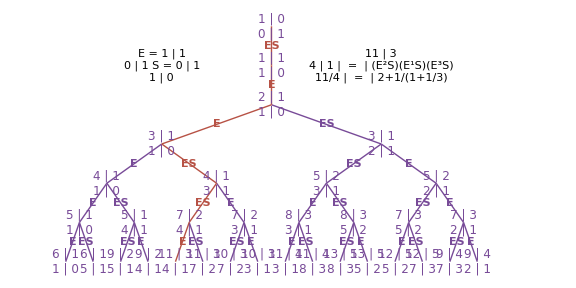

```mathematica
Txb0031EuclideanTree=Ch2EuclideanTree;txbExport[Txb0031EuclideanTree]
```